# Computational Nuclear Physics: Project 1

## Deuterium binding energy calculations assuming a square well

## 1) Taking as a given that Ebind=-2.2245ev and calculating the parameters V0 and L

## Constants

```mathematica
(*Hbar*c^2 in fm*MeV*)
HbarTimesCSq=197.3269631^2; 
(*mc^2 MeV*)
NeutronMass=939.56542052;
(*Ebind*)
DeuteriumBindingEnergy=-2.2245;
NumberOfSolutions=10;
```

## Calculating the limits of V0*L^2 so we have one energy state

The lowest value of V0L^2 so we only have one energy state.

```mathematica
V0TimesLSqLower=V0TimesLSq/.Solve[Pi^2/4==2*NeutronMass*V0TimesLSq/HbarTimesCSq,V0TimesLSq][[1]];
Print["The lowest limit for V0*L^2 so we have just one energy state is: ",V0TimesLSqLower," ev*fm^2."]
```

The lowest limit for V0*L^2 so we have just one energy state is: 51.1276 ev*fm^2.

The  highest  value  of  V0L^2  so  we  only  have  one  energy  state.

```mathematica
V0TimesLSqHigher=V0TimesLSq/.Solve[9Pi^2/4==2*NeutronMass*V0TimesLSq/HbarTimesCSq,V0TimesLSq][[1]];
Print["The highest limit for V0*L^2 so we have just one energy state is: ",V0TimesLSqHigher," ev*fm^2."]
```

The highest limit for V0*L^2 so we have just one energy state is: 460.149 ev*fm^2.

## Dividing V0*L^2 into 10 subspaces and calculating ξ1

We take 10 values of V0*L^2 between the highest and lowest limits of V0*L^2.

```mathematica
V0TimesLSqValues=Subdivide[V0TimesLSqLower,V0TimesLSqHigher,NumberOfSolutions-1];
Print["The 10 values of V0*L^2 we get are: ",V0TimesLSqValues]
```

The 10 values of V0*L^2 we get are: {51.1276,96.5744,142.021,187.468,232.915,278.362,323.808,369.255,414.702,460.149}

The functions n1(ξ) and n2(ξ) are defined

```mathematica
n1=-ksi*Cot[ksi];
n2=Sqrt[2*NeutronMass*V0TimesLSqValues/HbarTimesCSq-ksi^2];
```

Ksi1 is a table that will hold the solutions of n1(ξ)=n2(ξ)

```mathematica
ksi1=Table[0,NumberOfSolutions];
```

n1(ξ),n2(ξ) are ploted. ξ1 is calculated by the points where the 2 functions meet.

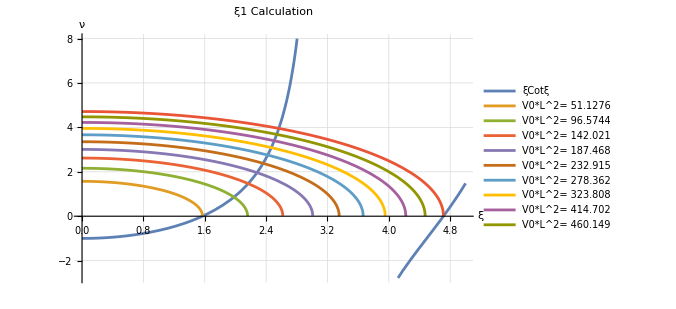

```mathematica
Plot[{n1,n2},{ksi,0,5},  PlotLabel -> Style["ξ1 Calculation", 18, Bold],
PlotLegends->{"ξCotξ","V0*L^2= "<>ToString[V0TimesLSqValues[[1]]],"V0*L^2= "<>ToString[V0TimesLSqValues[[2]]],"V0*L^2= "<>ToString[V0TimesLSqValues[[3]]],"V0*L^2= "<>ToString[V0TimesLSqValues[[4]]],"V0*L^2= "<>ToString[V0TimesLSqValues[[5]]],"V0*L^2= "<>ToString[V0TimesLSqValues[[6]]],"V0*L^2= "<>ToString[V0TimesLSqValues[[7]]],"V0*L^2= "<>ToString[V0TimesLSqValues[[9]]],"V0*L^2= "<>ToString[V0TimesLSqValues[[10]]]},
  AxesLabel -> {Style["ξ",13,Bold],Style[ "ν",13,Bold]},
  GridLines -> Automatic,
  GridLinesStyle -> Directive[Gray, Dashed],
  ImageSize -> 500]
```

ξ1 (the points of intersection) are calculated and saved in ksi1.

```mathematica
For[i=1,i<=NumberOfSolutions,i++,n2Solve=n2[[i]];
ksi1[[i]]=Re[ksi/.FindRoot[n1==n2Solve,{ksi,2},MaxIterations->10000]]
]
```

```mathematica
Print["The value of ξ1 for each value of V0*L^2 is: ",ksi1]
```

The value of ξ1 for each value of V0*L^2 is: {1.5708,1.98033,2.16672,2.28088,2.36049,2.42031,2.46749,2.50601,2.53827,2.56582}

## Calculation of V0 and L by solving the system |Ebind|=V0-(hbar*c^2)/(2 μc^2 L^2)ξ1 and V0L^2=a

The right side of the equation |Ebind|(V0,L^2) for each of the ξ1s:

```mathematica
EnergyEqRightSide=V0-ksi1^2*HbarTimesCSq/(2*NeutronMass*L^2)
```

{-51.1276/L^2+V0,-81.2627/L^2+V0,-97.2799/L^2+V0,-107.8/L^2+V0,-115.457/L^2+V0,-121.383/L^2+V0,-126.162/L^2+V0,-130.131/L^2+V0,-133.503/L^2+V0,-136.417/L^2+V0}

The values of L and V0 will be saved in these two lists:

```mathematica
LValues=Table[0,NumberOfSolutions];
V0Values=Table[0,NumberOfSolutions];
```

L and V0 are calculated by solving the system |Ebind(V0,L)|=a and V0*L^2=b

```mathematica
For[i=1,i<=NumberOfSolutions,i++,
LValues[[i]]=L/.Solve[{Abs[DeuteriumBindingEnergy]==EnergyEqRightSide[[i]],V0TimesLSqValues[[i]]==V0*L^2,L>=0,V0>=0},{L,V0}];

V0Values[[i]]=V0/.Solve[{Abs[DeuteriumBindingEnergy]==EnergyEqRightSide[[i]],V0TimesLSqValues[[i]]==V0*L^2,L>=0,V0>=0},{L,V0}];
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

The lists are flattened so they are in the right form

```mathematica
LValues=Flatten[LValues];
Print["The values of L for each value of TraditionalForm`ξ1 are:", LValues]
V0Values=Flatten[V0Values];
Print["The values of V0 for each value of TraditionalForm`ξ1 are:", V0Values]
```

The values of L for each value of TraditionalForm`ξ1 are:{L,2.62359,4.48475,5.98446,7.26649,8.40048,9.42602,10.368,11.2432,12.0636}

The values of V0 for each value of TraditionalForm`ξ1 are:{V0,14.0304,7.06118,5.23452,4.41111,3.94458,3.64444,3.43507,3.28061,3.16188}

We see that we dont have a solution for the first value of ξ1, so we replace the first element of each list:

```mathematica
LValues=Delete[LValues,1];
V0Values=Delete[V0Values,1];
```

Plotting L(V0) that gives us |Ebind|=2.22 ev

We create the points (V0,L)

```mathematica
V0Ldat=Table[{V0Values[[i]],LValues[[i]]},{i,Length[LValues]}]
```

{{14.0304,2.62359},{7.06118,4.48475},{5.23452,5.98446},{4.41111,7.26649},{3.94458,8.40048},{3.64444,9.42602},{3.43507,10.368},{3.28061,11.2432},{3.16188,12.0636}}

We  create  the  plot  of  L (V0)

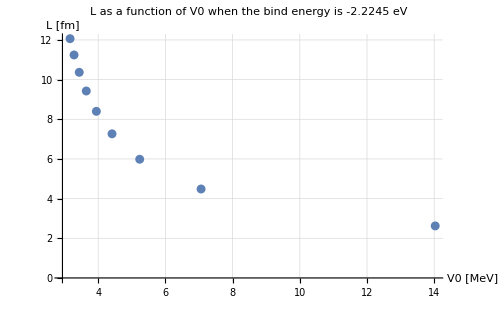

```mathematica
ListPlot[V0Ldat,
PlotLabel -> Style["L as a function of V0 when the bind energy is "<>ToString[DeuteriumBindingEnergy]<>" eV", 15, Bold],AxesLabel -> {Style["V0 [MeV]",13,Bold],Style[ "L [fm]",13,Bold]},
  GridLines -> Automatic,
  GridLinesStyle -> Directive[Gray, Dashed],
  ImageSize -> 500]
```

## The calculation and plot of the radius aspect of the first 3 wavefunctions R(r).

#### The number of wavefunctions we want to plot and γ^2=(2 μc^2)/(hbar^2*c^2)|Ebind| and κ^2=(2 μc^2)/(hbar^2*c^2)*(V0-|Ebind|)

```mathematica
NumberOfWavefunctions=3;
GammaValueSquared=2*NeutronMass*Abs[DeuteriumBindingEnergy]/HbarTimesCSq;
Print["The value of TraditionalForm`γ^2 is: ",GammaValueSquared]
KappaValuesSquared=2*NeutronMass*(V0Values-Abs[DeuteriumBindingEnergy])/HbarTimesCSq;
Print["The values of TraditionalForm`k^2 for each of the 9 pairs of (V0,L) is: ",KappaValuesSquared]
```

The value of TraditionalForm`γ^2 is: 0.107354

The values of TraditionalForm`k^2 for each of the 9 pairs of (V0,L) is: {0.569748,0.233417,0.145263,0.105525,0.0830105,0.0685259,0.0584219,0.0509675,0.0452376}

#### The values of the normalizations constants A and B. Lambda=√(1/Lambda)

```mathematica
AValues=Table[0,NumberOfWavefunctions];
BValues=Table[0,NumberOfWavefunctions];
Lambda=Table[0,NumberOfWavefunctions];
```

#### Lambda, A and B are calculated for the first 3 values of (L,V0,γ,κ) by normalizing our wavefunctions

```mathematica
For[i=1,i<=NumberOfWavefunctions,i++,

Lambda[[i]]=Integrate[(Sin[Sqrt[KappaValuesSquared[[i]]]*r])^2,{r,0,LValues[[i]]}]+Integrate[(Sin[Sqrt[KappaValuesSquared[[i]]]*LValues[[i]]])^2/Exp[-2*Sqrt[GammaValueSquared]*LValues[[i]]]*Exp[-2*Sqrt[GammaValueSquared]*r],{r,LValues[[i]],Infinity}];
AValues[[i]]=Sqrt[1/Lambda[[i]]];
BValues[[i]]=AValues[[i]]*Sin[Sqrt[KappaValuesSquared[[i]]]*LValues[[i]]]/Exp[-Sqrt[GammaValueSquared]*LValues[[i]]]
]
```

```mathematica
Print["The values of the normalization constant A are:", AValues]
```

The values of the normalization constant A are:{0.593619,0.515136,0.470451}

```mathematica
Print["The values of the normalization constant B are:", BValues]
```

The values of the normalization constant B are:{1.28632,1.85318,2.53469}

#### The radius component of the wavefunction R=n/r in area A (r<L) and area B (r>L) where na(r)=A*Sin(kr), nB(r)=B*e^-γr

```mathematica
nA=AValues*Sin[Sqrt[KappaValuesSquared[[Range[1,NumberOfWavefunctions]]]]*r];
nB=BValues*Exp[-Sqrt[GammaValueSquared]*r];
```

#### The table where the function R(r) will be saved.

```mathematica
R=Table[0,NumberOfWavefunctions];
```

#### We calculate R (r) for the first 3 pairs

```mathematica
For[i=1,i<=NumberOfWavefunctions,i++,
R[[i]]=Piecewise[{{nA[[i]]/r,0<=r<=LValues[[i]]},{nB[[i]]/r,r>=LValues[[i]]}}];
]
```

#### We plot all 3 R(r)

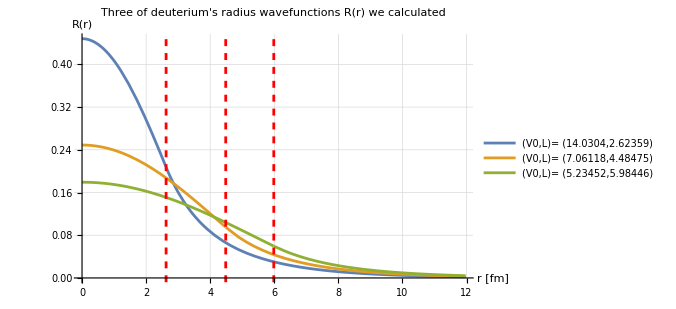

```mathematica
Plot[R,{r,0,2*LValues[[NumberOfWavefunctions]]},
Epilog->{Thickness[0.004],Dashed,Red,Line[{{LValues[[1]],-1},{LValues[[1]],1}}],Line[{{LValues[[2]],-1},{LValues[[2]],1}}],Line[{{LValues[[3]],-1},{LValues[[3]],1}}]},
PlotLabel -> Style["Three of deuterium's radius wavefunctions R(r) we calculated", 15, Bold],
PlotLegends->{"(V0,L)= ("<>ToString[V0Values[[1]]]<>","<>ToString[LValues[[1]]]<>")",
"(V0,L)= ("<>ToString[V0Values[[2]]]<>","<>ToString[LValues[[2]]]<>")",
"(V0,L)= ("<>ToString[V0Values[[3]]]<>","<>ToString[LValues[[3]]]<>")"},
AxesLabel -> {Style["r [fm]",13,Bold],Style[ "R(r)",13,Bold]},
  GridLines -> Automatic,
  GridLinesStyle -> Directive[Gray, Dashed],
  ImageSize -> 500]
```

## We calculate <r>^2 so we can get an ideaof deuterium’s size acording to the wavefunctions we calculated

```mathematica
AveragerSquared=Table[0,NumberOfWavefunctions];
For[i=1,i<=NumberOfWavefunctions,i++,
AveragerSquared[[i]]=Integrate[(nA[[i]])^2*r^2,{r,0,LValues[[i]]}]+Integrate[(nB[[i]])^2*r^2,{r,LValues[[i]],Infinity}];
]
```

#### <r> or deuterium’s size acording to our wavefunctions

```mathematica
Averager=Sqrt[AveragerSquared];
Print["The average value of r, calculated from each one of our 3 warefunctions is:",Averager," fm."];
```

The average value of r, calculated from each one of our 3 warefunctions is:{3.27031,4.17385,4.92969} fm.

## 2) Chosing V0 and L so VO*L^2 has the aprropiate values so we only have one state. We calculate such state

#### We chose the values 1 MeV≤V0≤ 20 Mev with a step of dV0=0.5 Mev and 2 fm ≤L≤5 fm with a step of dL=0.2 fm and save the results in the appropiate lists

```mathematica
V0Values2=Range[1,20,0.5];
LValues2=Range[2,5,0.2];
```

#### We define the apropiate lists where we will save all the needed coontities those are the values of V0*L^2 for every pair of L and V0 we geverated. If V0^L^2 is within the propper margins we save the value of L in LValuesPropper and the value of V0 in V0ValuesPropper. We also save ξ_1 and |E_bind|. With those values of L and V0 we calculate ξ1 by solving n1(ξ)=n2(ξ). Finally |E_bind|=V_0-(hbar*c)^2/(2 μc^2)ξ_1

```mathematica
V0TimesLSqValues2=Table[0,Length[V0Values2],Length[LValues2]];
ksi12={};
BindingEnergyValue={};
LValuesPropper={};
V0ValuesPropper={};
```

#### Here LValuePropper and V0ValuesPropper are generated. With LValuePropper and V0ValuesPrpper, we calculate ξ1 by solving n1(ξ)=n2(ξ). Finally |E_bind|=V_0-(hbar*c)^2/(2 μc^2)ξ_1

```mathematica
For[i=1,i<=Length[V0Values2],i++,
For[j=1,j<=Length[LValues2],j++,
V0TimesLSqValues2[[i]][[j]]=V0Values2[[i]]*LValues2[[j]]^2;
If[V0TimesLSqLower<=V0TimesLSqValues2[[i]][[j]]<=V0TimesLSqHigher,
AppendTo[V0ValuesPropper,V0Values2[[i]]];
AppendTo[LValuesPropper,LValues2[[j]]];
n2Solve2=Sqrt[2*NeutronMass*V0TimesLSqValues2[[i]][[j]]/HbarTimesCSq-ksi^2];

AppendTo[ksi12,Re[ksi/.FindRoot[n1==n2Solve2,{ksi,2},MaxIterations->10000]]];
AppendTo[BindingEnergyValue,Last[V0ValuesPropper]-HbarTimesCSq*Last[ksi12]/(2*NeutronMass*Last[LValues2]^2)];
]
]
]
```

```mathematica
V0LBindingEnergyData=Table[{V0ValuesPropper[[i]],LValuesPropper[[i]],BindingEnergyValue[[i]]},{i,Length[V0ValuesPropper]}];
```

```mathematica
BindingEnergyPlot=ListPointPlot3D[V0LBindingEnergyData,PlotStyle->PointSize[Medium],PlotLabel -> Style["The binding energy calculated for different values of V0 and L", 15, Bold],
AxesLabel->{Style["V0 (MeV)",13,Bold],Style["L (fm)",13,Bold],Style["Binding Energy (Mev)",13,Bold]},
BoxRatios->{1,1,1},
  ImageSize -> 500]
PlanePlot=ContourPlot3D[z==DeuteriumBindingEnergy,{x,Min[V0ValuesPropper],Max[V0ValuesPropper]},{y,Min[LValuesPropper],Max[LValuesPropper]},{z,0,5}]
```

-Graphics3D-

-Graphics3D-